```mathematica
<<xlr8r.m
```

xCellerator 0.88 (18-July-2012) loaded 21 July 2012 at 11:32 GMT-06:60 using Mathematica 8.0 for Linux x86 (64-bit) (October 10, 2011) (Version 8., Release 4) (MathSBML 1203-002)
GNU General Public License (GPL) Terms Apply.

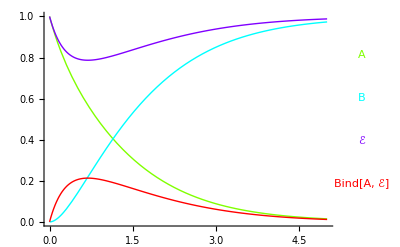

```mathematica
model={{Overscript[A⇄B, ℰ],a,d,k}};
IC={A-> 1,B-> 0,ℰ-> 1};
parameters={a-> 1, d-> .1, k-> 2}; 
sim=run[model,timeSpan-> 5,initialConditions-> IC, 
rates-> parameters];
runPlot[sim]
```

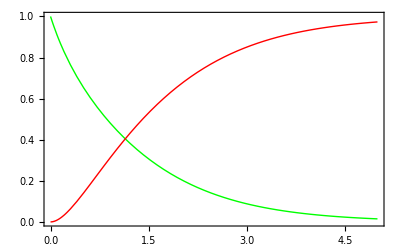

```mathematica
runPlot[sim,{A,B},holdLegend-> True,Frame-> True,PlotStyle-> {Brown, Green},BaseStyle-> {FontSize-> 18,FontFamily->"Verdana"}]
```